```mathematica
Clear["Global`*"];
```

#### relativistic degrees of freedom in the plasma

We use the data given in 2005.03544 
[Ken’ichi Saikawa, Satoshi Shirai, 
“Precise WIMP Dark Matter Abundance and Standard Model Thermodynamics”,
JCAP, 2020 (2020)]
(available at https://member.ipmu.jp/satoshi.shirai/DM2020/)
that describe the function shown in Fig.5 in 1803.01038.

```mathematica
(*this comment we can decide to keep, to change or to drop*)
```

```mathematica
gsstab=Import[NotebookDirectory[]<>"/data/gss_Tord.txt", "Table"];
gstarsdata=Table[{gsstab[[i, 1]],gsstab[[i, 2]]} ,{i, 1, Length[gsstab]}];
gs=Interpolation[gstarsdata, InterpolationOrder->2];
```

```mathematica
(*the plots can be omitted in the final version of the code if we think there is no interest in keeping them*)
```

```mathematica
LogLinearPlot[gs[T], {T, 0,10}, PlotLabel->"Entropy relativistic d.o.f.",PlotLegends->{"g_s[T]"}, (*AxesLabel->{"T[GeV]", "g_(*s)"}*) FrameLabel->{Style[HoldForm["T[GeV]"],20,Black,FontFamily->"Times"],Style[HoldForm["g_(*s)"],20,Black,FontFamily->"Times"]}];
```

```mathematica
LogLogPlot[{gs[T], gs'[T]}, {T, 0,10},PlotRange->All, PlotLabel->"Entropy relativistic d.o.f.",PlotLegends->{"g_s[T]", "g_s'[T]"}, (*AxesLabel->{"T[GeV]", "g_(*s)"}*) FrameLabel->{Style[HoldForm["T [GeV]"],20,Black,FontFamily->"Times"],Style[HoldForm[""],20,Black,FontFamily->"Times"]}];
```

#### Active neutrinos interaction rate

Interaction rate coefficient for electron neutrinos digitizing Fig. 1 in 1512.05369 
[Alexander Merle, Aurel Schneider, Maximilian Totzauer, 
“Dodelson-Widrow production of sterile neutrino Dark Matter with non-trivial initial abundance”, 
JCAP, 04, 003 (2016)]

```mathematica
Cedata = Import[NotebookDirectory[]<>"/data/C_e.txt", "Table"];
Ce=Interpolation[Cedata, InterpolationOrder->1];
```

```mathematica
(*the plot can be omitted in the final version of the code if we think there is no interest in keeping it*)
```

```mathematica
LogLinearPlot[Ce[T], {T, 0,10}, PlotLabel->"Interaction rate coefficient C_e", (*AxesLabel->{"T[GeV]", "C_e"}*) FrameLabel->{Style[HoldForm["T [GeV]"],20,Black,FontFamily->"Times"],Style[HoldForm["C_e"],20,Black,FontFamily->"Times"]}];
```

#### Constants

```mathematica
GF=1.166*10^-5;
MPl=1.22* 10^19;
ηB= 6.05*10^−10;
mZ= 91.1876;
mW= 80.379; (*last 4 quantities in GeV*)
Tf=.001 ;(*final temperature *)
```

## Resonances at Dodelson-Widrow Mechanism with Pseudoscalar NSI

RHS[r,T,ϵ,m_ϕ,m_s,sin^22θ] is the function we integrate to get f(r,T). i.e, RHS ⧦ ⅆf/dT

```mathematica
RHS[r_,T_,ϵ_,mϕ_,ms_,sin22θ_]:=Sqrt[90/(8 π^3*gs[T])] MPl/T^3(1+T/3(gs'[T]/gs[T]))*((Ce[T]+(7π*ϵ^2)/180)/4 GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)*
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ/ ((ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ+ 
((Ce[T]+(7π*ϵ^2)/180)GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)^2/4 + 
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T))+ (Sqrt[2] *GF*2*Zeta[3]*T^3*ηB)/(4*π^2) + (8*Sqrt[2]*GF)/(3 mZ^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*3/4 Zeta[3]/π^2 T^3*7/180 π^4/Zeta[3] T + (8*Sqrt[2]*GF)/(3 mW^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*2/(2 π^2)T^3*5.6822*T-(7*Sqrt[2]*π^2*GF*ϵ)/(45*mϕ^2)*(gs[T]/gs[Tf])^(1/3)*r*T*T^4 )^2)*
(Exp[(gs[T]/gs[Tf])^(1/3)r]+1)^-1
```

```mathematica
Manipulate[LogLogPlot[ {RHS[r,T,ϵ,mϕ,ms,sin22θ]},{T,0.01,10},AxesLabel->{"T","df/dT"},PlotLabel->"DW+Pseudoscalar NSI",PlotRange->Full],{{mϕ,50.},10,100,Row[{Slider[Dynamic[Log10[#],(mϕ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{ϵ,1.},0.1,100,Row[{Slider[Dynamic[Log10[#],(ϵ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{r,1.},0.01,10,Row[{Slider[Dynamic[Log10[#],(r=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{ms,7.1*10^-6},1*10^-6,100*10^-6,Row[{Slider[Dynamic[Log10[#],(ms=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{sin22θ,1.*10^-4},1*10^-10,100*10^-6,Row[{Slider[Dynamic[Log10[#],(sin22θ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

## Dodelson-Widrow Mechanism with Scalar NSI (no resonance)

RHS[r,T,ϵ,m_ϕ,m_s,sin^22θ] is the function we integrate to get f(r,T). i.e, RHS ⧦ ⅆf/dT

```mathematica
RHSscalar[r_,T_,ϵ_,mϕ_,ms_,sin22θ_]:=Sqrt[90/(8 π^3*gs[T])] MPl/T^3(1+T/3(gs'[T]/gs[T]))*((Ce[T]+(7π*ϵ^2)/180)/4 GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)*
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ/ ((ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T)))^2*sin22θ+ 
((Ce[T]+(7π*ϵ^2)/180)GF^2 T^4*(gs[T]/gs[Tf])^(1/3) r *T)^2/4 + 
(ms^2/(2 ((gs[T]/gs[Tf])^(1/3)r*T))+ (Sqrt[2] *GF*2*Zeta[3]*T^3*ηB)/(4*π^2) + (8*Sqrt[2]*GF)/(3 mZ^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*3/4 Zeta[3]/π^2 T^3*7/180 π^4/Zeta[3] T + (8*Sqrt[2]*GF)/(3 mW^2)*(gs[T]/gs[Tf])^(1/3)*r*T*2*2/(2 π^2)T^3*5.6822*T+(7*Sqrt[2]*π^2*GF*ϵ)/(45*mϕ^2)*(gs[T]/gs[Tf])^(1/3)*r*T*T^4 )^2)*
(Exp[(gs[T]/gs[Tf])^(1/3)r]+1)^-1
```

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[r,T,ϵ,mϕ,ms,sin22θ]},{T,0.01,10},AxesLabel->{"T","df/dT"},PlotLabel->"DW+Scalar NSI",PlotRange->Full],{{mϕ,50.},10,100,Row[{Slider[Dynamic[Log10[#],(mϕ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{ϵ,1.},0.1,100,Row[{Slider[Dynamic[Log10[#],(ϵ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{r,1.},0.01,10,Row[{Slider[Dynamic[Log10[#],(r=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{ms,7.1*10^-6},1*10^-6,100*10^-6,Row[{Slider[Dynamic[Log10[#],(ms=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&},{{sin22θ,1.*10^-4},1*10^-10,100*10^-6,Row[{Slider[Dynamic[Log10[#],(sin22θ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=10GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

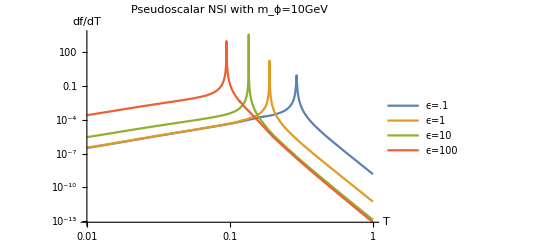

```mathematica
LogLogPlot[ {RHS[1,T,.1,10,7.1*10^-6,10^-10],RHS[1,T,1,10,7.1*10^-6,10^-10],RHS[1,T,10,10,7.1*10^-6,10^-10],RHS[1,T,100,10,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"ϵ=.1","ϵ=1","ϵ=10","ϵ=100"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with m_ϕ=10GeV"]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=100GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

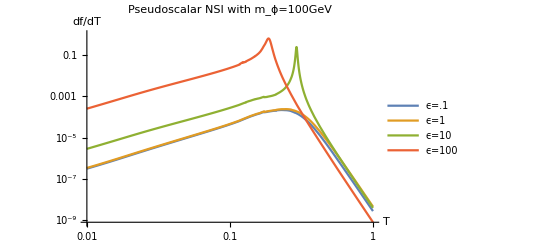

```mathematica
LogLogPlot[ {RHS[1,T,.1,100,7.1*10^-6,10^-10],RHS[1,T,1,100,7.1*10^-6,10^-10],RHS[1,T,10,100,7.1*10^-6,10^-10],RHS[1,T,100,100,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"ϵ=.1","ϵ=1","ϵ=10","ϵ=100"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with m_ϕ=100GeV"]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=1000GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

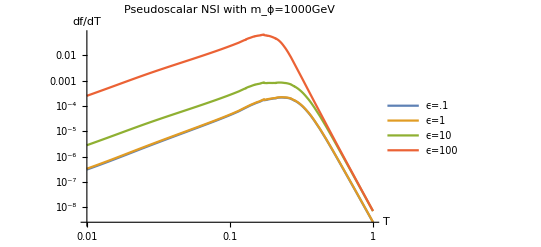

```mathematica
LogLogPlot[ {RHS[1,T,.1,1000,7.1*10^-6,10^-10],RHS[1,T,1,1000,7.1*10^-6,10^-10],RHS[1,T,10,1000,7.1*10^-6,10^-10],RHS[1,T,100,1000,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"ϵ=.1","ϵ=1","ϵ=10","ϵ=100"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with m_ϕ=1000GeV"]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=10GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHS[1,T,ϵ,10,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with m_ϕ=10GeV"],{{ϵ,10.},0.01,100,Row[{Slider[Dynamic[Log10[#],(ϵ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=100GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHS[1,T,ϵ,100,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with m_ϕ=100GeV"],{{ϵ,10.},0.01,100,Row[{Slider[Dynamic[Log10[#],(ϵ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=1, m_s=7.1keV, sin^2 2θ= 10^-10)

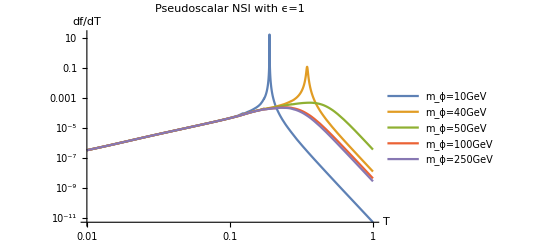

```mathematica
LogLogPlot[ {RHS[1,T,1,10,7.1*10^-6,10^-10],RHS[1,T,1,40,7.1*10^-6,10^-10],RHS[1,T,1,50,7.1*10^-6,10^-10],RHS[1,T,1,100,7.1*10^-6,10^-10],RHS[1,T,1,250,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"m_ϕ=10GeV","m_ϕ=40GeV","m_ϕ=50GeV","m_ϕ=100GeV","m_ϕ=250GeV"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=1"]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=10, m_s=7.1keV, sin^2 2θ= 10^-10)

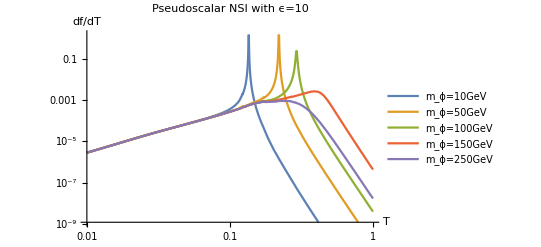

```mathematica
LogLogPlot[ {RHS[1,T,10,10,7.1*10^-6,10^-10],RHS[1,T,10,50,7.1*10^-6,10^-10],RHS[1,T,10,100,7.1*10^-6,10^-10],RHS[1,T,10,150,7.1*10^-6,10^-10],RHS[1,T,10,250,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"m_ϕ=10GeV","m_ϕ=50GeV","m_ϕ=100GeV","m_ϕ=150GeV","m_ϕ=250GeV"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=10"]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=100, m_s=7.1keV, sin^2 2θ= 10^-10)

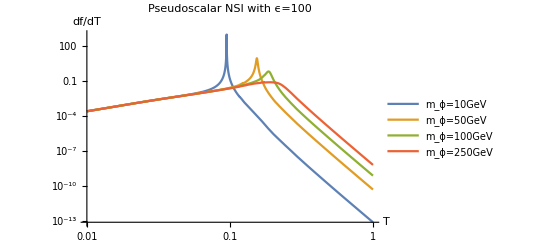

```mathematica
LogLogPlot[ {RHS[1,T,100,10,7.1*10^-6,10^-10],RHS[1,T,100,50,7.1*10^-6,10^-10],RHS[1,T,100,100,7.1*10^-6,10^-10],RHS[1,T,100,250,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"m_ϕ=10GeV","m_ϕ=50GeV","m_ϕ=100GeV","m_ϕ=250GeV"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=100"]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=1, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHS[1,T,1,mϕ,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=1"],{{mϕ,100.},10,1000,Row[{Slider[Dynamic[Log10[#],(mϕ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=10, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHS[1,T,10,mϕ,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=10"],{{mϕ,100.},10,1000,Row[{Slider[Dynamic[Log10[#],(mϕ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying r (fixed m_ϕ=10, ϵ=.10, m_s=7.1keV, sin^2 2θ= 10^-10)

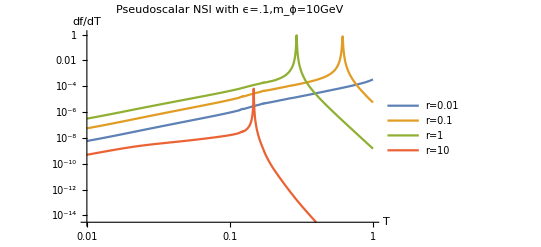

```mathematica
LogLogPlot[ {RHS[0.01,T,.10,10,7.1*10^-6,10^-10],RHS[.1,T,.10,10,7.1*10^-6,10^-10],RHS[1,T,.10,10,7.1*10^-6,10^-10],RHS[10,T,.10,10,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"r=0.01","r=0.1","r=1","r=10"},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=.1,m_ϕ=10GeV"]
```

#### df/dT Vs T for varying r (fixed m_ϕ=10, ϵ=.10, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHS[x,T,.10,10,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=.1,m_ϕ=10GeV"],{{x,10.},0.01,10.,Row[{Slider[Dynamic[Log10[#],(x=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying r (fixed m_ϕ=10, ϵ=1, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHS[x,T,1,10,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Pseudoscalar NSI with ϵ=1,m_ϕ=10GeV"],{{x,10.},0.01,10.,Row[{Slider[Dynamic[Log10[#],(x=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=10GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

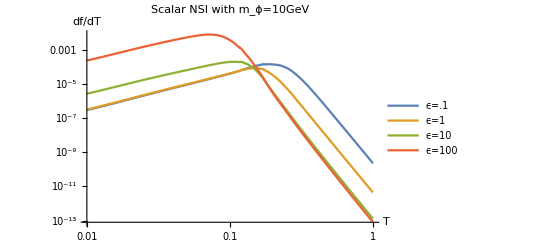

```mathematica
LogLogPlot[ {RHSscalar[1,T,.1,10,7.1*10^-6,10^-10],RHSscalar[1,T,1,10,7.1*10^-6,10^-10],RHSscalar[1,T,10,10,7.1*10^-6,10^-10],RHSscalar[1,T,100,10,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"ϵ=.1","ϵ=1","ϵ=10","ϵ=100"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with m_ϕ=10GeV"]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=100GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

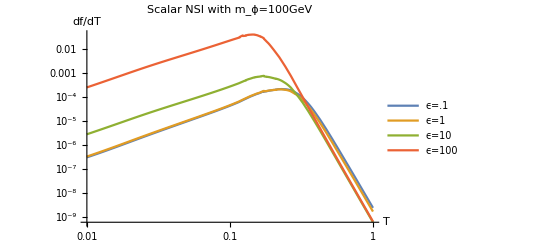

```mathematica
LogLogPlot[ {RHSscalar[1,T,.1,100,7.1*10^-6,10^-10],RHSscalar[1,T,1,100,7.1*10^-6,10^-10],RHSscalar[1,T,10,100,7.1*10^-6,10^-10],RHSscalar[1,T,100,100,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"ϵ=.1","ϵ=1","ϵ=10","ϵ=100"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with m_ϕ=100GeV"]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=1000GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

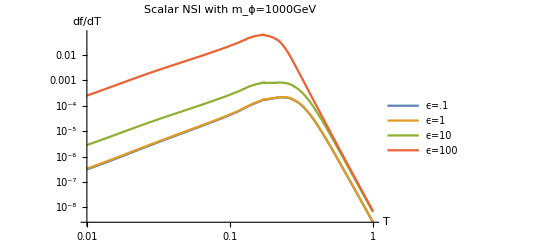

```mathematica
LogLogPlot[ {RHSscalar[1,T,.1,1000,7.1*10^-6,10^-10],RHSscalar[1,T,1,1000,7.1*10^-6,10^-10],RHSscalar[1,T,10,1000,7.1*10^-6,10^-10],RHSscalar[1,T,100,1000,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"ϵ=.1","ϵ=1","ϵ=10","ϵ=100"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with m_ϕ=1000GeV"]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=10GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[1,T,ϵ,10,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with m_ϕ=10GeV"],{{ϵ,10.},0.01,100,Row[{Slider[Dynamic[Log10[#],(ϵ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying ϵ (fixed r=1, m_ϕ=100GeV, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[1,T,ϵ,100,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with m_ϕ=100GeV"],{{ϵ,10.},0.01,100,Row[{Slider[Dynamic[Log10[#],(ϵ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=1, m_s=7.1keV, sin^2 2θ= 10^-10)

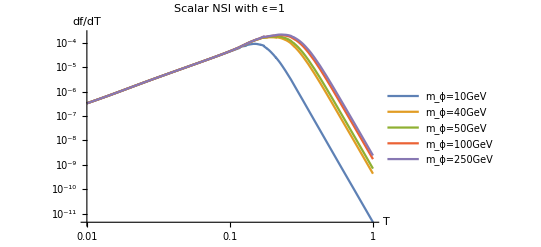

```mathematica
LogLogPlot[ {RHSscalar[1,T,1,10,7.1*10^-6,10^-10],RHSscalar[1,T,1,40,7.1*10^-6,10^-10],RHSscalar[1,T,1,50,7.1*10^-6,10^-10],RHSscalar[1,T,1,100,7.1*10^-6,10^-10],RHSscalar[1,T,1,250,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"m_ϕ=10GeV","m_ϕ=40GeV","m_ϕ=50GeV","m_ϕ=100GeV","m_ϕ=250GeV"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=1"]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=10, m_s=7.1keV, sin^2 2θ= 10^-10)

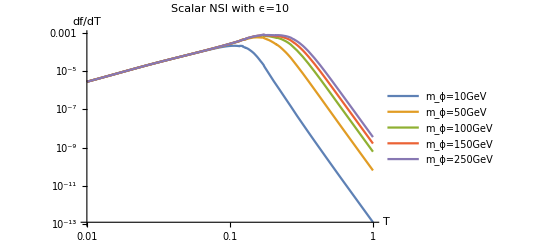

```mathematica
LogLogPlot[ {RHSscalar[1,T,10,10,7.1*10^-6,10^-10],RHSscalar[1,T,10,50,7.1*10^-6,10^-10],RHSscalar[1,T,10,100,7.1*10^-6,10^-10],RHSscalar[1,T,10,150,7.1*10^-6,10^-10],RHSscalar[1,T,10,250,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"m_ϕ=10GeV","m_ϕ=50GeV","m_ϕ=100GeV","m_ϕ=150GeV","m_ϕ=250GeV"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=10"]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=100, m_s=7.1keV, sin^2 2θ= 10^-10)

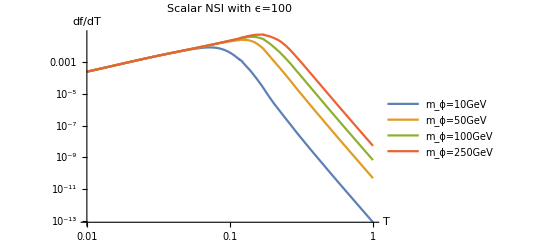

```mathematica
LogLogPlot[ {RHSscalar[1,T,100,10,7.1*10^-6,10^-10],RHSscalar[1,T,100,50,7.1*10^-6,10^-10],RHSscalar[1,T,100,100,7.1*10^-6,10^-10],RHSscalar[1,T,100,250,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"m_ϕ=10GeV","m_ϕ=50GeV","m_ϕ=100GeV","m_ϕ=250GeV"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=100"]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=1, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[1,T,1,mϕ,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=1"],{{mϕ,100.},10,1000,Row[{Slider[Dynamic[Log10[#],(mϕ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying m_ϕ (fixed r=1, ϵ=10, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[1,T,10,mϕ,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=10"],{{mϕ,100.},10,1000,Row[{Slider[Dynamic[Log10[#],(mϕ=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying r (fixed m_ϕ=10, ϵ=.10, m_s=7.1keV, sin^2 2θ= 10^-10)

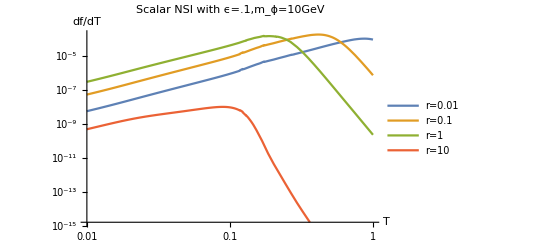

```mathematica
LogLogPlot[ {RHSscalar[0.01,T,.10,10,7.1*10^-6,10^-10],RHSscalar[.1,T,.10,10,7.1*10^-6,10^-10],RHSscalar[1,T,.10,10,7.1*10^-6,10^-10],RHSscalar[10,T,.10,10,7.1*10^-6,10^-10]},{T,0.01,1},PlotLegends->{"r=0.01","r=0.1","r=1","r=10"},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=.1,m_ϕ=10GeV"]
```

#### df/dT Vs T for varying r (fixed m_ϕ=10, ϵ=.10, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[x,T,.10,10,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=.1,m_ϕ=10GeV"],{{x,10.},0.01,10.,Row[{Slider[Dynamic[Log10[#],(x=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```

#### df/dT Vs T for varying r (fixed m_ϕ=10, ϵ=1, m_s=7.1keV, sin^2 2θ= 10^-10)

```mathematica
Manipulate[LogLogPlot[ {RHSscalar[x,T,1,10,7.1*10^-6,10^-10]},{T,0.01,1},AxesLabel->{"T","df/dT"},PlotLabel->"Scalar NSI with ϵ=1,m_ϕ=10GeV"],{{x,10.},0.01,10.,Row[{Slider[Dynamic[Log10[#],(x=10^#)&],Log10[#2]]," ",InputField[#,Appearance->"Frameless",BaseStyle->"Label"]}]&}]
```